# Coupled catastrophes: sudden shifts cascade and hop among interdependent systems

## Charles D. Brummitt, George Barnett, Raissa M. D’Souza

## About this document

This document provides the code used to make the figures for the empirical data in the open access paper

Brummitt, C. D., Barnett, G., & D’Souza, R. M. (2015). Coupled catastrophes: sudden shifts cascade and hop among interdependent systems. Journal of the Royal Society Interface, 12(112), 20150712. http://doi.org/10.1098/rsif.2015.0712

### Contact information

Charlie Brummitt: c.brummitt@columbia.edu

## Facebook graph among countries involved in the Arab Spring

### Data

#### Facebook 2012 data

We scraped data from the Facebook blog:

Newman M. 2012 Interactive: mapping the world’s friendships. http://www.facebookstories.com/ stories/1574/ (accessed 17 March 2014).

Import the raw data:

```mathematica
FacebookRawData=Import[FileNameJoin[{NotebookDirectory[],"data","Facebook_Friends_dirty.xlsx"}]];
```

List of all countries in the Facebook data:

```mathematica
countries=Rest[FacebookRawData⟦1,1⟧];
```

Convert this raw data to a list of directed edges:

```mathematica
FacebookRawEdgeList=(Property[First[#]->#⟦2,1⟧,EdgeWeight->#⟦2,2⟧]&/@Transpose[{Table[First[#],{Length[Last[#]]}],Last[#]}]&)/@
({First[#],Select[Transpose[{countries,Rest[#]}],Last[#]≠""&]}&/@FacebookRawData⟦1,2;;-1⟧);
```

Flatten the list of edges and reverse those edges so that the arrows indicate direction of influence (so that A -> B means that A is on B’s top-five list of countries to which it has the most cross-border friendships):

```mathematica
FacebookRawEdgeListReversed=Flatten[FacebookRawEdgeList,1]/.{Property[x_->y_,EdgeWeight->w_]->Property[y->x,EdgeWeight->w]};
```

#### dates of protests

See http://en. wikipedia.org/wiki/Arab_Spring#Summary _of _ conflicts_by _country (accessed May 14, 2014).

```mathematica
datesOfProtests=Map[{#⟦1⟧,If[#⟦2⟧===None,#⟦2⟧,DateList[#⟦2⟧]],If[#⟦2⟧===None,#⟦2⟧,AbsoluteTime@DateList[#⟦2⟧]]}&,{{"Tunisia","18 December 2010"},{"Algeria","29 December 2010"},{"Jordan","14 January 2011"},{"Oman","17 January 2011"},{"Egypt","25 January 2011"},{"Yemen","27 January 2011"},{"Bahrain","14 February 2011"},{"Libya","17 February 2011"},{"Syria","11 March 2011"},{"Saudi Arabia","15 March 2011"},{"Albania",None},{"Iran",None},{"Qatar",None},{"United Arab Emirates",None},{"Djibouti","28 January 2011"},{"Iraq","23 December 2012"},{"Israel","15 May 2011"},{"Kuwait","19 February 2011"},{"Mauritania","25 February 2011"},{"Morocco","20 February 2011"},{"Palestinian Territory","4 September 2012"},{"Somalia","28 January 2011"},{"Sudan","30 January 2011"},{"Lebanon","27 February 2011"}}];
datesOfProtestsRules=(First[#]->Part[#,2]&)/@datesOfProtests;
datesOfProtestsAssociation=Association[datesOfProtestsRules];
```

```mathematica
countriesWithProtests=Sort[First/@Select[datesOfProtests,Last[#]=!=None&]];
countriesThatDidNotProtest=Complement[countries,First/@datesOfProtests];
```

Rescale these protest dates so that we can easily plot them on a horizontal axis:

```mathematica
rescaledProtestOutbreakDatesRules=(Rule@@#)&/@({First[#],(N@Last[#]-Min[Last/@Select[datesOfProtests,Last[#]=!=None&]])/((Max[#]-Min[#])&[Last/@Select[datesOfProtests,Last[#]=!=None&]])}&/@Select[datesOfProtests,Last[#]=!=None&]);
```

We may consider also showing other countries that could have played a role in propagating influence to protest but did not have protests according to Wikipedia:

```mathematica
rescaledProtestOutbreakDatesRulesAll=rescaledProtestOutbreakDatesRules~Join~{"Albania"->2.,"Iran"->2.,"United Arab Emirates"->2.,"Qatar"->2.};
```

```mathematica
countriesInvolvedInArabSpring={"Albania","Algeria","Bahrain","Djibouti","Egypt","Iran","Iraq","Israel","Jordan","Kuwait","Lebanon","Libya","Mauritania","Morocco","Oman","Palestinian Territory","Saudi Arabia","Somalia","Sudan","Syria","Tunisia","Yemen","United Arab Emirates","Qatar"};
```

#### unemployment data from the World Bank

Source: The World Bank, 2010. http://data.worldbank.org. (accessed 14 May 2014).

```mathematica
convertWorldBankCountryNamesToFacebookNames={"Syrian Arab Republic"->"Syria","Egypt, Arab Rep."->"Egypt","Yemen, Rep."->"Yemen","West Bank and Gaza"->"Palestinian Territory","Iran, Islamic Rep."->"Iran"};
```

```mathematica
actualUnemploymentData=Import[FileNameJoin[{NotebookDirectory[],"data","sl.uem.totl.zs_Indicator_en_csv_v2","sl.uem.totl.zs_Indicator_en_csv_v2.csv"}]];
```

```mathematica
unemploymentRatioIn2010={First[#],#⟦-5⟧}&/@actualUnemploymentData⟦4;;-1⟧;
```

```mathematica
unemploymentRatioIn2010ForCountriesInvolvedInArabSpringRules=Rule@@#&/@Select[unemploymentRatioIn2010/.convertWorldBankCountryNamesToFacebookNames, MemberQ[countriesInvolvedInArabSpring,First[#]]&](*~Join~{{"Palestinian Territory",24.}}*)
```

{Albania→14.2,United Arab Emirates→4,Bahrain→7.5,Djibouti→,Algeria→10,Egypt→9,Iran→13.5,Iraq→15.2,Israel→6.6,Jordan→12.5,Kuwait→1.6,Lebanon→8.9,Libya→8.6,Morocco→9.1,Mauritania→31.1,Oman→8.3,Qatar→0.4,Saudi Arabia→5.5,Sudan→14.8,Somalia→7.6,Syria→8.4,Tunisia→13,Palestinian Territory→23.7,Yemen→17.8}

Djbouti had 54% unemployment in 2010. Citation: http://www.tradingeconomics.com/djibouti/unemployment-rate

```mathematica
unemploymentRatioIn2010ForCountriesInvolvedInArabSpringRules=(Rule@@#)&/@ReplacePart[Select[unemploymentRatioIn2010/.convertWorldBankCountryNamesToFacebookNames, MemberQ[countriesInvolvedInArabSpring,First[#]]&],{4,2}-> 54.]
```

{Albania→14.2,United Arab Emirates→4,Bahrain→7.5,Djibouti→54.,Algeria→10,Egypt→9,Iran→13.5,Iraq→15.2,Israel→6.6,Jordan→12.5,Kuwait→1.6,Lebanon→8.9,Libya→8.6,Morocco→9.1,Mauritania→31.1,Oman→8.3,Qatar→0.4,Saudi Arabia→5.5,Sudan→14.8,Somalia→7.6,Syria→8.4,Tunisia→13,Palestinian Territory→23.7,Yemen→17.8}

```mathematica
Length@unemploymentRatioIn2010ForCountriesInvolvedInArabSpring
```

0

```mathematica
Length@countriesInvolvedInArabSpring
```

24

#### income data from the World Bank: GDP per capita, PPP (constant 2011 international $)

Source: The World Bank, 2010. http://data.worldbank.org. (accessed 14 May 2014).

File: ny.gdp.pcap.cd_Indicator_en_csv_v2

GDP per capita in current USD: 
http://data.worldbank.org/indicator/NY.GDP.PCAP.CD

Description: “GDP per capita based on purchasing power parity (PPP). PPP GDP is gross domestic product converted to international dollars using purchasing power parity rates. An international dollar has the same purchasing power over GDP as the U.S. dollar has in the United States. GDP at purchaser’s prices is the sum of gross value added by all resident producers in the economy plus any product taxes and minus any subsidies not included in the value of the products. It is calculated without making deductions for depreciation of fabricated assets or for depletion and degradation of natural resources. Data are in constant 2011 international dollars.”

```mathematica
gdpPerCapitaData=Import[FileNameJoin[{NotebookDirectory[],"data","ny.gdp.pcap.cd_Indicator_en_csv_v2","ny.gdp.pcap.cd_Indicator_en_csv_v2.csv"}]];
```

```mathematica
gdpPerCapita2010={First[#],#⟦-5⟧}&/@gdpPerCapitaData⟦4;;-1⟧;
```

```mathematica
gdpPerCapitaIn2010ForCountriesInvolvedInArabSpring=Select[gdpPerCapita2010/.convertWorldBankCountryNamesToFacebookNames, MemberQ[countriesInvolvedInArabSpring,First[#]]&]
```

{{Albania,3764.33},{United Arab Emirates,34048.5},{Bahrain,20546.},{Djibouti,},{Algeria,4349.57},{Egypt,2803.53},{Iran,5674.92},{Iraq,4612.52},{Israel,30389.1},{Jordan,4370.72},{Kuwait,40090.7},{Lebanon,8551.85},{Libya,},{Morocco,2822.73},{Mauritania,1017.17},{Oman,20983.9},{Qatar,72773.3},{Saudi Arabia,19326.6},{Sudan,1422.37},{Somalia,},{Syria,},{Tunisia,4206.78},{Palestinian Territory,},{Yemen,1400.67}}

```mathematica
Length@%
```

24

```mathematica
gdpPerCapitaIn2010ForCountriesInvolvedInArabSpringRules=(Rule@@#)&/@gdpPerCapitaIn2010ForCountriesInvolvedInArabSpring;
```

Patch the missing data from the world bank with WolframAlpha data for Djbouti, Libya, Syria, Somalia (query for 2011 given that the WorldBank data is for 2011 PPP):

```mathematica
gdpPerCapitaIn2010ForCountriesInvolvedInArabSpring={{"Albania",3764.32634799148},{"United Arab Emirates",34048.5173453316},{"Bahrain",20545.9694536416},{"Djibouti",1464.},{"Algeria",4349.56932474256},{"Egypt",2803.53296265274},{"Iran",5674.92392735085},{"Iraq",4612.52347575944},{"Israel",30389.107581936},{"Jordan",4370.72103318115},{"Kuwait",40090.7462727442},{"Lebanon",8551.85241627055},{"Libya",5685.},{"Morocco",2822.73373914854},{"Mauritania",1017.16627752181},{"Oman",20983.9003354042},{"Qatar",72773.314202226},{"Saudi Arabia",19326.5825548176},{"Sudan",1422.3681025837},{"Somalia",145.1},{"Syria",2066.},{"Tunisia",4206.77992157625},{"Palestinian Territory",""},{"Yemen",1400.66768498865}}
```

{{Albania,3764.33},{United Arab Emirates,34048.5},{Bahrain,20546.},{Djibouti,1464.},{Algeria,4349.57},{Egypt,2803.53},{Iran,5674.92},{Iraq,4612.52},{Israel,30389.1},{Jordan,4370.72},{Kuwait,40090.7},{Lebanon,8551.85},{Libya,5685.},{Morocco,2822.73},{Mauritania,1017.17},{Oman,20983.9},{Qatar,72773.3},{Saudi Arabia,19326.6},{Sudan,1422.37},{Somalia,145.1},{Syria,2066.},{Tunisia,4206.78},{Palestinian Territory,},{Yemen,1400.67}}

```mathematica
gdpPerCapitaIn2010ForCountriesInvolvedInArabSpringRules=(Rule@@#)&/@gdpPerCapitaIn2010ForCountriesInvolvedInArabSpring;
```

#### gross national income (GNI) per capita, PPP

Source: The World Bank, 2010. http://data.worldbank.org. (accessed 14 May 2014).

“GNI per capita based on purchasing power parity (PPP). PPP GNI is gross national income (GNI) converted to international dollars using purchasing power parity rates.” 

http://data.worldbank.org/indicator/NY.GNP.PCAP.PP.CD

```mathematica
gniPerCapitaData=Import[FileNameJoin[{NotebookDirectory[],"data","ny.gnp.pcap.pp.cd_Indicator_en_csv_v2","ny.gnp.pcap.pp.cd_Indicator_en_csv_v2.csv"}]];
```

```mathematica
gniPerCapita2010={First[#],#⟦-5⟧}&/@gniPerCapitaData⟦4;;-1⟧;
```

```mathematica
gniPerCapitaIn2010ForCountriesInvolvedInArabSpring=Select[gniPerCapita2010/.convertWorldBankCountryNamesToFacebookNames, MemberQ[countriesInvolvedInArabSpring,First[#]]&]
```

{{Albania,8480},{United Arab Emirates,56260},{Bahrain,31820},{Djibouti,},{Algeria,12270},{Egypt,10360},{Iran,},{Iraq,12660},{Israel,27960},{Jordan,11000},{Kuwait,86560},{Lebanon,15580},{Libya,},{Morocco,6140},{Mauritania,2660},{Oman,43730},{Qatar,126620},{Saudi Arabia,45900},{Sudan,2860},{Somalia,},{Syria,},{Tunisia,9940},{Palestinian Territory,},{Yemen,4300}}

```mathematica
Length@%
```

24

```mathematica
gniPerCapitaIn2010ForCountriesInvolvedInArabSpringRules=(Rule@@#)&/@gniPerCapitaIn2010ForCountriesInvolvedInArabSpring;
```

#### internet penetration

Source: The World Bank, 2010. http://data.worldbank.org. (accessed 14 May 2014).

File: it.net.user.p2_Indicator_en_csv_v2

```mathematica
internetPenetrationData=Import[FileNameJoin[{NotebookDirectory[],"data","it.net.user.p2_Indicator_en_csv_v2","it.net.user.p2_Indicator_en_csv_v2.csv"}]];
```

```mathematica
internetPenetration2010={First[#],#⟦-5⟧}&/@internetPenetrationData⟦4;;-1⟧;
```

```mathematica
internetPenetrationIn2010ForCountriesInvolvedInArabSpring=Select[internetPenetration2010/.convertWorldBankCountryNamesToFacebookNames, MemberQ[countriesInvolvedInArabSpring,First[#]]&]
```

{{Albania,45},{United Arab Emirates,68},{Bahrain,55},{Djibouti,6.5},{Algeria,12.5},{Egypt,31.42},{Iran,14.7},{Iraq,2.5},{Israel,67.5},{Jordan,27.2},{Kuwait,61.4},{Lebanon,43.68},{Libya,14},{Morocco,52},{Mauritania,4},{Oman,35.8278},{Qatar,81.6},{Saudi Arabia,41},{Sudan,16.7},{Somalia,},{Syria,20.7},{Tunisia,36.8},{Palestinian Territory,37.4},{Yemen,12.35}}

```mathematica
Length@%
```

24

Note: there is no data for Somalia. But http://en.wikipedia.org/wiki/Communications_in_Somalia says that Internet penetration is 1.2% in 2012 (accessed Sept. 12, 2014).

```mathematica
internetPenetrationIn2010ForCountriesInvolvedInArabSpringRules=(Rule@@#)&/@(internetPenetrationIn2010ForCountriesInvolvedInArabSpring/.{"Somalia",""}->{"Somalia",1.2});
```

#### unemployment of young men

Source: The World Bank, 2010. http://data.worldbank.org. (accessed 14 May 2014).

(% of male labor force ages 15-24) (modeled ILO estimate)
http://data.worldbank.org/indicator/SL.UEM.1524.MA.ZS

File: sl.uem.1524.ma.zs_Indicator_en_excel_v2.xls

```mathematica
youngMenUnemploymentData=Import[FileNameJoin[{NotebookDirectory[],"data","sl.uem.1524.ma.zs_Indicator_en_excel_v2.xls"}]];
```

```mathematica
youngMenUnemployment2010={First[#],#⟦-4⟧}&/@youngMenUnemploymentData⟦1,4;;-1⟧;
```

```mathematica
youngMenUnemployment2010ForCountriesInvolvedInArabSpring=Select[youngMenUnemployment2010/.convertWorldBankCountryNamesToFacebookNames, MemberQ[countriesInvolvedInArabSpring,First[#]]&]
```

{{Albania,27.3},{United Arab Emirates,8.1},{Bahrain,24.7},{Djibouti,},{Algeria,19.1},{Egypt,14.8},{Iran,25.2},{Iraq,28.6},{Israel,14.6},{Jordan,25.1},{Kuwait,11.},{Lebanon,23.1},{Libya,18.1},{Morocco,18.3},{Mauritania,47.9},{Oman,18.1},{Qatar,0.5},{Saudi Arabia,23.8},{Sudan,21.9},{Somalia,12.5},{Syria,15.5},{Tunisia,30.3},{Palestinian Territory,35.7},{Yemen,27.9}}

```mathematica
Length@%
```

24

```mathematica
youngMenUnemployment2010ForCountriesInvolvedInArabSpringRules=(Rule@@#)&/@youngMenUnemployment2010ForCountriesInvolvedInArabSpring;
```

#### political freedoms

```mathematica
freedomOfPressData=First@Import[FileNameJoin[{NotebookDirectory[],"data","freedom","freedom_of_press.xlsx"}],"Data"];
freedomOfPressDataRules=Module[{data=freedomOfPressData},Flatten[Table[{"country"->data⟦row,1⟧,"year"->IntegerPart[data⟦1,col⟧],"value"->data⟦row,col⟧},{row,2,Length[data]},{col,2,Length[First@data]}],1]];
```

```mathematica
politicalFreedomData=First@Import[FileNameJoin[{NotebookDirectory[],"data","freedom","political_freedom.xlsx"}],"Data"];
politicalFreedomDataRules=Module[{data=politicalFreedomData},Flatten[Table[{"country"->data⟦row,1⟧,"year"->IntegerPart[data⟦1,col⟧],"value"->data⟦row,col⟧},{row,2,Length[data]},{col,2,Length[First@data]}],1]];
```

```mathematica
webFreedomData=First@Import[FileNameJoin[{NotebookDirectory[],"data","freedom","web_freedom.xlsx"}],"Data"];
webFreedomDataRules=Module[{data=webFreedomData},Flatten[Table[{"country"->data⟦row,1⟧,"year"->IntegerPart[data⟦1,col⟧],"value"->data⟦row,col⟧},{row,2,Length[data]},{col,2,Length[First@data]}],1]];
```

```mathematica
civilLibertiesData=First@Import[FileNameJoin[{NotebookDirectory[],"data","freedom","civil_liberties.xlsx"}],"Data"];
civilLibertiesDataRules=Module[{data=civilLibertiesData},Flatten[Table[{"country"->data⟦row,1⟧,"year"->IntegerPart[data⟦1,col⟧],"value"->data⟦row,col⟧},{row,2,Length[data]},{col,2,Length[First@data]}],1]];
```

#### political freedoms (from the Freedom House website)

This spreadsheet has political rights and civil liberties data (and subcategories of that and F, PF, NF). The file civil_liberties_political_freedom.xls is from http://www.freedomhouse.org/report/freedom-world-aggregate-and-subcategory-scores #.VBLzlGRdUuF Accessed September 12, 2014.

```mathematica
civilLibertiesPoliticalFreedomData=First@Import[FileNameJoin[{NotebookDirectory[],"data","freedom","civil_liberties_political_freedom.xls"}],"Data"];
```

```mathematica
civilLibertiesPoliticalFreedomDataAssociation=Association[(First[#]-><|(Rule@@#&)/@Transpose[{(*civilLibertiesPoliticalFreedomData⟦18,2;;-1⟧*){"Political Rights","Civil Liberties","StatusFPFNF","Electoral Process","Political Pluralism and Participation","Functioning of Government","Freedom of Expression and Belief","Associational and Organizational Rights","Rule of Law","Personal Autonomy and Individual Rights"},Rest[#]}]|>)&/@civilLibertiesPoliticalFreedomData⟦19;;-1⟧];
```

#### world press freedom index

File: press_freedom_index.csv
World Press freedom Index was downloaded from http://rsf.org/index2014/en-index2014.php
Then click on the link Download the index csv file. We will use the data from 2013 (7th column “sco2013”)

```mathematica
pressFreedomIndexData=Import[FileNameJoin[{NotebookDirectory[],"data","freedom","press_freedom_index.csv"}],"Data"];
```

```mathematica
pressFreedomIndexDataAssociation=Association[MapThread[#1-><|"pressFreedom2013"->#2|>&,{pressFreedomIndexData⟦2;;-1,2⟧,pressFreedomIndexData⟦2;;-1,7⟧}]];
```

#### “fuzzy” data from Hussain and Howard

This data was copied from Table 1 in the paper

Hussain, M. M., & Howard, P. N. (2013). What Best Explains Successful Protest Cascades? ICTs and the Fuzzy Causes of the Arab Spring. International Studies Review, 15(1), 48–66. http://doi.org/10.1111/misr.12020

This data consists of “scores” that are computed from data or estimated by experts, and they are intended to be used for comparison.

```mathematica
fuzzyDataString="Country Gdppc Gini Unemp Urban Youth Mobile Internet Fuel Pol Success

Algeria 0.58 0.37 0.42 0.47 0.32 0.47 0.32 1 0.83 0.55

Bahrain 0.84 0.42 0.58 0.89 0.26 0.68 0.89 0.58 0.11 0.2

Djibouti 0.16 0.74 1 0.63 0.74 0.05 0.16 0.01 0.83 0.3

Egypt 0.32 0.21 0.26 0.26 0.58 0.37 0.37 0.42 0.56 0.95

Iraq 0.05 0.11 0.74 0.42 0.89 0.42 0.79 0.37 0.94 0.3

Jordan 0.53 0.58 0.47 0.01 0.63 0.63 0.47 0.05 0.56 0.6

Kuwait 0.89 0.01 0.05 1 0.16 0.84 0.74 0.89 0.28 0.6

Lebanon 0.63 0.95 0.32 0.84 0.21 0.26 0.58 0.11 1 0.6

Libya 0.68 0.42 0.84 0.68 0.42 0.95 0.11 0.95 0.28 0.8

Mauritania 0.11 0.68 0.84 0.21 0.84 0.32 0.05 0.26 0.67 0.4

Morocco 0.42 0.79 0.37 0.37 0.37 0.53 0.68 0.21 0.44 0.6

Oman 0.79 0.21 0.58 0.58 0.47 0.89 0.84 0.68 0.11 0.6

Qatar 1 0.79 0.01 0.95 0.01 0.74 0.95 0.63 0.01 0.5

Saudi 0.74 0.21 0.16 0.74 0.53 1 0.47 0.79 0.01 0.6

Somalia 0.01 0.01 0.95 0.11 1 0.01 0.01 0.16 0.5 0.5

Sudan 0.26 1 0.79 0.16 0.79 0.11 0.21 0.74 0.67 0.55

Syria 0.37 0.42 0.21 0.32 0.68 0.21 0.42 0.47 0.28 0.7

Tunisia 0.47 0.79 0.53 0.53 0.11 0.58 0.63 0.32 0.5 0.95

UAE 0.95 0.11 0.11 0.79 0.05 0.79 1 0.53 0.11 0.4

Yemen 0.21 0.58 0.58 0.05 0.95 0.16 0.26 0.84 0.67 0.95";
```

```mathematica
fuzzyColumns=First@Partition[StringSplit[fuzzyDataString],11]
```

{Country,Gdppc,Gini,Unemp,Urban,Youth,Mobile,Internet,Fuel,Pol,Success}

Missing countries in the fuzzy data:

```mathematica
Complement[countriesInvolvedInArabSpring,First/@Rest[Partition[StringSplit[fuzzyDataString],11]]/.{"Saudi"->"Saudi Arabia","UAE"->"United Arab Emirates"}]
```

{Albania,Iran,Israel,Palestinian Territory}

Fuzzy data using rules:

```mathematica
fuzzyDataRules=MapThread[#1->(Thread[Rest@fuzzyColumns->#2])&,{First/@Rest[Partition[StringSplit[fuzzyDataString],11]]/.{"Saudi"->"Saudi Arabia","UAE"->"United Arab Emirates"},Rest/@Rest[Partition[StringSplit[fuzzyDataString],11]]}];
```

```mathematica
gdppcFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Gdppc"/.Last/@fuzzyDataRules))];
giniFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Gini"/.Last/@fuzzyDataRules))];
unempFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Unemp"/.Last/@fuzzyDataRules))];
urbanFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Urban"/.Last/@fuzzyDataRules))];
youthFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Youth"/.Last/@fuzzyDataRules))];
mobileFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Mobile"/.Last/@fuzzyDataRules))];
internetFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Internet"/.Last/@fuzzyDataRules))];
fuelFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Fuel"/.Last/@fuzzyDataRules))];
polFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Pol"/.Last/@fuzzyDataRules))];
successFuzzy=Thread[First/@fuzzyDataRules->(ToExpression/@("Success"/.Last/@fuzzyDataRules))];
```

#### Gini coefficient

Data is from the World Factbook https://www.cia.gov/library/publications/the-world-factbook/rankorder/2172rank.html

```mathematica
GINIrawData="1\tLesotho\t             63.2
2\tSouth Africa\t             63.1
3\tBotswana\t             63.0
4\tSierra Leone\t             62.9
5\tCentral African Republic\t             61.3
6\tNamibia\t             59.7
7\tHaiti\t             59.2
8\tHonduras\t             57.7
9\tZambia\t             57.5
10\tColombia\t             55.9
11\tGuatemala\t             55.1
12\tHong Kong\t             53.7
13\tParaguay\t             53.2
14\tChile\t             52.1
15\tPanama\t             51.9
16\tBrazil\t             51.9
17\tPapua New Guinea\t             50.9
18\tSwaziland\t             50.4
19\tCosta Rica\t             50.3
20\tGambia, The\t             50.2
21\tZimbabwe\t             50.1
22\tSri Lanka\t             49.0
23\tEcuador\t             48.5
24\tMexico\t             48.3
25\tPeru\t             48.1
26\tMadagascar\t             47.5
27\tChina\t             47.3
28\tDominican Republic\t             47.2
29\tBolivia\t             47.0
30\tEl Salvador\t             46.9
31\tRwanda\t             46.8
32\tSingapore\t             46.3
33\tMalaysia\t             46.2
34\tGeorgia\t             46.0
35\tSouth Sudan\t             46.0
36\tArgentina\t             45.8
37\tMozambique\t             45.6
38\tJamaica\t             45.5
39\tBulgaria\t             45.3
40\tUruguay\t             45.3
41\tUnited States\t             45.0
42\tPhilippines\t             44.8
43\tCameroon\t             44.6
44\tGuyana\t             44.6
45\tIran\t             44.5
46\tUganda\t             44.3
47\tNigeria\t             43.7
48\tKenya\t             42.5
49\tBurundi\t             42.4
50\tRussia\t             42.0
51\tCote d'Ivoire\t             41.5
52\tSenegal\t             41.3
53\tDjibouti\t             40.9
54\tMorocco\t             40.9
55\tTurkmenistan\t             40.8
56\tNicaragua\t             40.5
57\tTurkey\t             40.2
58\tMali\t             40.1
59\tTunisia\t             40.0
60\tJordan\t             39.7
61\tBurkina Faso\t             39.5
62\tGhana\t             39.4
63\tGuinea\t             39.4
64\tThailand\t             39.4
65\tMacedonia\t             39.2
66\tMauritania\t             39.0
67\tVenezuela\t             39.0
68\tMalawi\t             39.0
69\tMauritius\t             39.0
70\tBhutan\t             38.7
71\tPortugal\t             38.5
72\tSerbia\t             38.0
73\tCambodia\t             37.9
74\tYemen\t             37.7
75\tIsrael\t             37.6
76\tJapan\t             37.6
77\tTanzania\t             37.6
78\tVietnam\t             37.6
79\tMaldives\t             37.4
80\tIndia\t             36.8
81\tUzbekistan\t             36.8
82\tIndonesia\t             36.8
83\tLaos\t             36.7
84\tMongolia\t             36.5
85\tBenin\t             36.5
86\tNew Zealand\t             36.2
87\tBosnia and Herzegovina\t             36.2
88\tLithuania\t             35.5
89\tAlgeria\t             35.3
90\tLatvia\t             35.2
91\tMacau\t             35.0
92\tAlbania\t             34.5
93\tGreece\t             34.3
94\tTaiwan\t             34.2
95\tPoland\t             34.1
96\tNiger\t             34.0
97\tIreland\t             33.9
98\tAzerbaijan\t             33.7
99\tKyrgyzstan\t             33.4
100\tMoldova\t             33.0
101\tEthiopia\t             33.0
102\tNepal\t             32.8
103\tTajikistan\t             32.6
104\tUnited Kingdom\t             32.3
105\tCanada\t             32.1
106\tBangladesh\t             32.1
107\tSpain\t             32.0
108\tCroatia\t             32.0
109\tItaly\t             31.9
110\tTimor-Leste\t             31.9
111\tEstonia\t             31.3
112\tKorea, South\t             31.1
113\tCyprus\t             31.0
114\tArmenia\t             30.9
115\tNetherlands\t             30.9
116\tEgypt\t             30.8
117\tFrance\t             30.6
118\tEuropean Union\t             30.6
119\tPakistan\t             30.6
120\tAustralia\t             30.3
121\tKosovo\t             30.0
122\tKazakhstan\t             28.9
123\tSwitzerland\t             28.7
124\tUkraine\t             28.2
125\tBelgium\t             28.0
126\tIceland\t             28.0
127\tRomania\t             27.4
128\tBelarus\t             27.2
129\tMalta\t             27.1
130\tGermany\t             27.0
131\tFinland\t             26.8
132\tAustria\t             26.3
133\tSlovakia\t             26.0
134\tLuxembourg\t             26.0
135\tNorway\t             25.0
136\tCzech Republic\t             24.9
137\tDenmark\t             24.8
138\tHungary\t             24.7
139\tMontenegro\t             24.3
140\tSlovenia\t             23.7
141\tSweden\t             23.0";
```

```mathematica
GINIdataRules=Rule[#⟦1⟧,ToExpression[#⟦2⟧]]&/@Partition[StringTrim/@Drop[StringSplit[GINIrawData,"\t"|"\n"],{1,-1,3}],2];
```

We need to add data from the World Peace Index for the countries with missing data in the CIA World Factbook. Below we grab data from the last column in http://en.wikipedia.org/wiki/List_of_countries _by _income _equality #List

```mathematica
CPIGINI={"Bahrain"->36.0,"Kuwait"->30,"Oman"->32,"Saudi Arabia"->32,"Sudan"->51,"United Arab Emirates"->31};
```

#### food price index

The data is from: http://faostat.fao.org/site/683/DesktopDefault.aspx?PageID=683# ancor
Accessed 6/20/14.

Countries: | Algeria | Bahrain | Egypt | Iran (Islamic Republic of) | Iraq | Israel | Jordan | Kuwait | Lebanon | Lebanon, Beyrouth | Mauritania | Morocco | Oman | Oman, Muscat | Pakistan | Qatar | Saudi Arabia, All cities | Saudi Arabia, Middle income group | Syrian Arab Republic | Syrian Arab Republic, Damas | Tunisia | Yemen |

Missing: UAE, Sudan

Description: “Consumer price indices (CPIs) measure changes over time in the general level of prices of consumer goods and services that households acquire, use or pay for consumption. This is done by measuring the cost of purchasing a fixed basket of consumer goods and services of constant quality and similar characteristics, with the products in the basket being selected to be representative of households’ expenditure during a year or other specified period.”

```mathematica
foodData2010=Import[FileNameJoin[{NotebookDirectory[],"data","foodindex","foodindex_2010.csv"}],"Data"];
foodIndex2010Rules=(#⟦1,1⟧->Identity[#⟦1,-1⟧]&)/@(StringSplit/@Take[foodData2010,{3,-1,2}]);
```

### Analysis

#### create the Facebook graph for all countries (run this before making Figure 4)

Create the graph of cross-border links for all countries:

```mathematica
FacebookGraphReversed=Graph[FacebookRawEdgeListReversed];
```

Here’s the subgraph induced by the countries with protests:

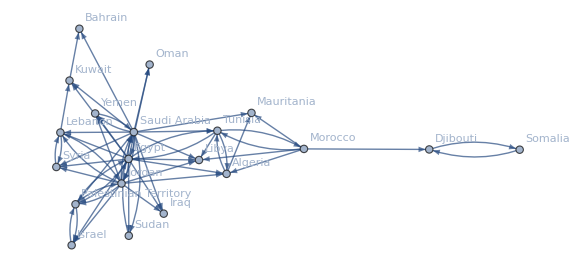

```mathematica
SetProperty[Subgraph[FacebookGraphReversed,countriesWithProtests],{VertexLabels->"Name",ImagePadding->20,ImageSize->Large}]
```

#### code to make Figure 4

```mathematica
ClearAll@visualizeFacebookGraphForThePaper
```

```mathematica
internetPenetrationIn2010ForCountriesInvolvedInArabSpringRules
```

```mathematica
visualizeFacebookGraphForThePaper[countriesToExamineInput_,yaxisLabel_,vertexSize_,OptionsPattern[]]:=Module[{graph,countriesToExamine,(*countriesToExamine=Cases[countriesWithProtests,Except["Palestinian Territory"|"Iraq"|"Israel"]],*)xaxis,yaxis,(*yaxisLabel,*)(*vertexSize,*)vertexSizeData,coord,coordDate,stretchFactor=OptionValue["HorizontalStretch"],fs=14,fsTicks=11,font="Times",vertexSizeRules,vertexStyleRules,vertexSizeInset,aspectRatio,linearFit,linearFitDateVersusYAxis,countriesRepresentativeOfVertexSize,vertexSizeLegendPosition=OptionValue["VertexSizeLegendPosition"]},

aspectRatio=OptionValue["AspectRatio"];
countriesToExamine=countriesToExamineInput;

yaxis=Select[FilterRules[Switch[yaxisLabel,
"Internet penetration",internetPenetrationIn2010ForCountriesInvolvedInArabSpringRules,
"unemployment",unemploymentRatioIn2010ForCountriesInvolvedInArabSpringRules,
"GDP per capita",gdpPerCapitaIn2010ForCountriesInvolvedInArabSpringRules,
"GNI per capita",gniPerCapitaIn2010ForCountriesInvolvedInArabSpringRules,
"Gini coefficient",GINIdataRules~Join~CPIGINI,
"unemployment of young men (age 15–34)",youngMenUnemployment2010ForCountriesInvolvedInArabSpringRules
,"freedom of press",(("country"/.#)->("value"/.#))&/@Select[freedomOfPressDataRules,("year"/.#)==2010&]
,"political freedom",(("country"/.#)->("value"/.#))&/@Select[politicalFreedomDataRules,("year"/.#)==2010&]
,"web freedom",(("country"/.#)->("value"/.#))&/@Select[webFreedomDataRules,("year"/.#)==2011&]
,"civil liberties",(("country"/.#)->("value"/.#))&/@Select[civilLibertiesDataRules,("year"/.#)==2010&]
,"GDP per capita (fuzzy)",gdppcFuzzy
,"Gini (fuzzy)",giniFuzzy
,"Unemployment (fuzzy)",unempFuzzy
,"Urban (fuzzy)",urbanFuzzy
,"Youth (fuzzy)",youthFuzzy
,"Mobile (fuzzy)",mobileFuzzy
,"Internet (fuzzy)",internetFuzzy
,"Fuel (fuzzy)",fuelFuzzy
,"Polity (1 = democracy, 0 = autocracy) (fuzzy)",polFuzzy
,"Success (fuzzy)",successFuzzy
,"food prices",foodIndex2010Rules
]
,countriesToExamine],Last[#]=!=""&];

countriesToExamine=Intersection[countriesToExamine,First/@yaxis];
xaxis=FilterRules[datesOfProtestsRules,countriesToExamine];
graph=Subgraph[FacebookGraphReversed,countriesToExamine];

vertexSizeData=Select[FilterRules[Switch[vertexSize,
"Internet penetration",internetPenetrationIn2010ForCountriesInvolvedInArabSpringRules,
"unemployment",unemploymentRatioIn2010ForCountriesInvolvedInArabSpringRules,
"GDP per capita",gdpPerCapitaIn2010ForCountriesInvolvedInArabSpringRules,
"GNI per capita",gniPerCapitaIn2010ForCountriesInvolvedInArabSpringRules,
"Gini coefficient",GINIdataRules~Join~CPIGINI,
"unemployment of young men (age 15–34)",youngMenUnemployment2010ForCountriesInvolvedInArabSpringRules
,"freedom of press",(("country"/.#)->("value"/.#))&/@Select[freedomOfPressDataRules,("year"/.#)==2010&]
,"political freedom",(("country"/.#)->("value"/.#))&/@Select[politicalFreedomDataRules,("year"/.#)==2010&]
,"web freedom",(("country"/.#)->("value"/.#))&/@Select[webFreedomDataRules,("year"/.#)==2011&]
,"civil liberties",(("country"/.#)->("value"/.#))&/@Select[civilLibertiesDataRules,("year"/.#)==2010&]
,"GDP per capita (fuzzy)",gdppcFuzzy
,"Gini (fuzzy)",giniFuzzy
,"Unemployment (fuzzy)",unempFuzzy
,"Urban (fuzzy)",urbanFuzzy
,"Youth (fuzzy)",youthFuzzy
,"Mobile (fuzzy)",mobileFuzzy
,"Internet (fuzzy)",internetFuzzy
,"Fuel (fuzzy)",fuelFuzzy
,"Polity (1 = democracy, 0 = autocracy) (fuzzy)",polFuzzy
,"Success (fuzzy)",successFuzzy
,"food prices (2010)",foodIndex2010Rules
,"food prices (2011)",foodIndex2010Rules
]
,countriesToExamine],Last[#]=!=""&];

vertexSizeRules=Map[(#⟦1⟧->(OptionValue["VertexSizeStretch"] {(#⟦2⟧)/Max[Last/@FilterRules[vertexSizeData,countriesToExamine]],(#⟦2⟧ OptionValue["VertexSizeVerticalStretch"](*/10*))/Max[Last/@FilterRules[vertexSizeData,countriesToExamine]]}))&,FilterRules[vertexSizeData,countriesToExamine]];

vertexStyleRules=((#->ColorData[OptionValue["ColorScheme"]][VertexOutDegree[graph,#]/Max[VertexOutDegree[graph]]]
)&/@VertexList[graph]);


vertexSizeInset=Labeled[Graphics[{Circle[{0,#⟦1,2⟧/4.},{#⟦1,2⟧,#⟦1,2⟧}/4.],Style[Text[ToString[Round@Last[#]]<>" %",{2,#⟦1,2⟧/4.+#⟦1,2⟧/4.*.9}],FontFamily->font]}&/@
({First[#],(*Part[#,Round[Length[#]*.25]],*)(*Part[#,IntegerPart[Length[#]/2.]],*)(*Part[#,IntegerPart[Length[#]*.85]],*)#⟦-2⟧,Last[#]}&[SortBy[List@@#&/@FilterRules[vertexSizeData,countriesToExamine],Last]]/.vertexSizeRules),ImageSize->75],Column[{Style["vertex size ∝",FontFamily->font],Style[vertexSize,FontFamily->font]}],Top];

(* coordinates of the countries in the plot *)
coord=(#->{((#/.(*xaxis*)FilterRules[rescaledProtestOutbreakDatesRulesAll,countriesToExamine])/.{2.->OptionValue["NoProtestPosition"]})*stretchFactor,#/.yaxis})&/@(First/@yaxis);
coordDate=(#->{(#/.xaxis),#/.yaxis})&/@(First/@FilterRules[yaxis,countriesToExamine]);

linearFit = LinearModelFit[Select[Last/@coord,First[#]≠2.&],{1,t},t];
linearFitDateVersusYAxis = LinearModelFit[{#⟦2⟧,AbsoluteTime[#⟦1⟧]}&/@Select[Last/@coordDate,First[#]=!=None&],{1,t},t];

(* pick two countries of intermediate and large vertex size in order to make a legend of vertex size *)
countriesRepresentativeOfVertexSize={#⟦Ceiling[Length[#]*.7],1⟧,#⟦-1,1⟧}&@SortBy[internetPenetrationIn2010ForCountriesInvolvedInArabSpringRules,Last];

Row[{Show[
ListPlot[Last/@coord,PlotRange->Full,Prolog->{If[Length[Intersection[countriesThatDidNotProtest,countriesToExamine]]>0,{Opacity[.3],Gray,Rectangle[{1/2(OptionValue["NoProtestPosition"]*stretchFactor+RankedMax[First/@Last/@coord,3]),-100},{(OptionValue["NoProtestPosition"]+1)*stretchFactor,1000}]},{}]},PlotMarkers->""],

SetProperty[HighlightGraph[graph,OptionValue["Highlight"]],
{VertexLabels->Table[v->Placed[Style[v/.{"United Arab Emirates"->"U.A.E."},FontFamily->font,FontSize->fsTicks+1],v/.OptionValue["VertexLabelPositions"]],{v,VertexList[graph]}],

VertexCoordinates->Evaluate[VertexList[graph]/.coord],
EdgeStyle->
((First[#]->Directive[Thickness[.0010(6-#⟦-1,2⟧)],Opacity[.5],Arrowheads[.03]])&/@Select[Flatten[FacebookRawEdgeList,1],MemberQ[countriesToExamine,#⟦1,1⟧]&&MemberQ[countriesToExamine,#⟦1,2⟧]&])
,VertexSize->vertexSizeRules,VertexStyle->vertexStyleRules}],

Graph[countriesRepresentativeOfVertexSize,{},VertexSize->FilterRules[vertexSizeRules,countriesRepresentativeOfVertexSize],VertexCoordinates->Table[v->vertexSizeLegendPosition+{0,First[v/.vertexSizeRules]},{v,countriesRepresentativeOfVertexSize}],VertexStyle->Directive[Opacity[0]],PlotLabel->Style[vertexSize,{FontSize->fs,FontFamily->"Times",Background->Yellow}],
VertexLabels->MapIndexed[#1⟦1⟧->Placed[Style[ToString[Round@#1⟦2⟧]<>"%",{FontSize->fsTicks,FontFamily->font}],{4.25-1.15 #2⟦1⟧,.45 #2⟦1⟧}]&,FilterRules[vertexSizeData,countriesRepresentativeOfVertexSize]]],

ImageSize->OptionValue["ImageSize"],AspectRatio->aspectRatio,PlotRangeClipping->True,PlotRangePadding->{{Scaled[.05],Scaled[.11]},If[Max[Last/@Last/@coord]>20,1,0]+{1.25,2}},Axes->None
,
Frame->True,FrameLabel->(Style[#,{FontSize->fs,FontFamily->Times}]&/@{"date of protest outbreak",yaxisLabel/.{"unemployment"|"unemployment estimated Djibouti"->"unemployment in 2010 (%)"}}),FrameTicks->{{Automatic,Automatic},{(
{(#/.FilterRules[rescaledProtestOutbreakDatesRulesAll,countriesToExamine]/.{2.->OptionValue["NoProtestPosition"]})*stretchFactor,

Rotate[Style[Which[(#/.xaxis)===None,"no\nprotest",MemberQ[OptionValue["DateTicksToExclude"],(#/.xaxis)],"",True,DateString[#/.xaxis,{"Day"," ","MonthNameShort"," ","YearShort"}]],FontFamily->font],If[(#/.xaxis)===None,0Degree,90Degree]]

}&/@(First/@xaxis)),Automatic}}
,Epilog->If[OptionValue["ShowFit"],{{Thick,Dashed,Darker@Green,Line[{{0,#[0]},{RankedMax[First/@Last/@coord,3],#[RankedMax[First/@Last/@coord,3]]}}]&@linearFit},Inset[TableForm[{Last[linearFitDateVersusYAxis["BestFitParameters"]]/60./60./24.,linearFit["RSquared"],linearFit["ANOVATableEntries"]⟦1,-1⟧},TableHeadings->{{"days per unit increase\nin "<>yaxisLabel,"R^2","p-value"},None}],OptionValue@"FitPosition"]},{}]
~Join~{Inset[Column[{Style["vertex diamter ∝",{FontSize->fsTicks,FontFamily->font}],Style[vertexSize,{FontSize->fsTicks,FontFamily->font}]},Alignment->Center,Spacings->{0,.1}],vertexSizeLegendPosition+{2,3.5}],Inset[SwatchLegend[Sequence@@Reverse@Transpose[Take[#,{1,-1,2}]&@SortBy[Union[{Style[VertexOutDegree[graph,#],{FontSize->fsTicks,FontFamily->font}],ColorData[OptionValue["ColorScheme"]][VertexOutDegree[graph,#]/Max[VertexOutDegree[graph]]]}&/@VertexList[graph]],First]],LegendLabel->Row[{Style["out",{FontSize->fsTicks,FontFamily->font}],Style["-",{FontSize->fsTicks-3.5,FontFamily->font}],Style["degree",{FontSize->fsTicks,FontFamily->font}]}],LegendMarkers->"Bubble"],Scaled[{1,1}],{1.25,1.15}],
If[OptionValue["ShowFacebookLegend"],Inset[Style["Facebook rank",{FontSize->fsTicks,FontFamily->font}],OptionValue["FacebookLegendLabelPosition"]],{}],If[OptionValue["ShowFacebookLegend"],Inset[Grid[({Graphics[{Directive[RGBColor[{119,131,163}/256.],Thickness[.0010(6-#)*15],Opacity[.8(*.6*)],Arrowheads[.33]],Arrow[{{0,0},{.3,0}}]},ImageSize->Automatic],Style[#,{FontSize->fsTicks,FontFamily->font}]}&/@Identity[Range[5]]),Spacings->{0,-20.5},Alignment->{Center,Center}],(OptionValue["FacebookLegendPosition"])],{}]}
,ImageMargins->OptionValue["ImageMargins"]]
},"\t"]
];
Options[visualizeFacebookGraphForThePaper]={"AspectRatio"->.5,"Highlight"->{},"NoProtestPosition"->.3,"HorizontalStretch"->200,"VertexSizeStretch"->1.,"VertexSizeVerticalStretch"->1.,"VertexLabelPositions"->{_->Below},"FitPosition"->Sequence[Scaled[{0,0}],{-1.5,-1.5}],"ShowFit"->True,"VertexSizeLegendPosition"->{2,1},"ColorScheme"->"TemperatureMap","ImageSize"->.98 {17.5/2.54*72},"DateTicksToExclude"->{{2011,2,19,0,0,0.},{2011,1,28,0,0,0.}},"ImageMargins"->Automatic,
"ShowFacebookLegend"->True,
"FacebookLegendPosition"->{.15,.31},"FacebookLegendLabelPosition"->{.15,.31}};
```

#### Figure 4: unemployment versus protest date, with the Facebook graph and Internet penetration shown

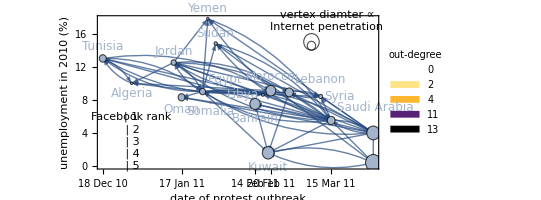

```mathematica
Module[{choices,countries,yaxisLabel},
choices={(*"Internet penetration","unemployment","GDP per capita","GNI per capita","Gini coefficient","unemployment of young men (age 15–34)","freedom of press","political freedom","web freedom","civil liberties"
,*)"GDP per capita (fuzzy)","Gini (fuzzy)","Unemployment (fuzzy)","Urban (fuzzy)","Youth (fuzzy)","Mobile (fuzzy)","Internet (fuzzy)","Fuel (fuzzy)","Polity (1 = democracy, 0 = autocracy) (fuzzy)","Success (fuzzy)"};
countries=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"|"Djibouti"]];

yaxisLabel="unemployment";
visualizeFacebookGraphForThePaper[countries,yaxisLabel,"Internet penetration","NoProtestPosition"->.14,"HorizontalStretch"->250,"Highlight"->(Style[#,Directive[Red,Opacity[1],(*AbsoluteThickness[3],*)Arrowheads[.065]]]&/@Reverse/@{"Saudi Arabia"->"Egypt","Bahrain"->"Saudi Arabia"}(*{"United Arab Emirates"->"Egypt","Bahrain"->"United Arab Emirates"}*)),"VertexSizeStretch"->1,"VertexLabelPositions"->{"Yemen"|"Tunisia"|"Jordan"|"Djibouti"|"Morocco"|"Sudan"->Above,"United Arab Emirates"|"Qatar"|"Syria"->After,"Saudi Arabia"|"Lebanon"|"Egypt"->{After,Above},"Libya"->Before,_->Below},"ShowFit"->False,"VertexSizeLegendPosition"->(*{3,1}*){27,14},
"ColorScheme"->{"SunsetColors","Reverse"},"ImageMargins"->3,"FacebookLegendPosition"->Scaled[{.12,.18}],"FacebookLegendLabelPosition"->Scaled[{.12,.34}]]
]
```

10 hop motifs (p-value 0.067, with null model in which protest dates are randomized)

Unemployment in 2010 has the largest coefficient of determination R^2=0.245. Each 1% of unemployment is associated with protests starting 3.2±1.5 days earlier (p-value 0.06). Based on the criterion for forward selection, no other covariate could be added to this model (unemployment and intercept) because the resulting adjusted R^2 are all less than 0.245.

Evidence of the domino hypothesis: Among countries that had protests, a majority of those countries share a border with at least one country whose protests began earlier, and a majority has a Facebook link from at least one country whose protest began earlier. These results are statistically significant compared with a null model of randomized protest dates. See endnote 9 of the paper.

## Motifs

### find hop motifs

#### code

For a given upstreamCountry, find all cascade hop motifs that have that country as the upstream country:

```mathematica
findCascadeHoppingsReversed[graph_,upstreamCountry_,vertexToTimeRules_]:=Module[{countriesPointingToInitialCountryCatastropheLater,secondNeighbors,result},

countriesPointingToInitialCountryCatastropheLater=Select[VertexList[graph](*First/@Cases[EdgeList[graph],upstreamCountry->_]*),
MemberQ[EdgeList[graph],upstreamCountry->#]&&
(#/.vertexToTimeRules)>(upstreamCountry/.vertexToTimeRules)&];

result=Reap[
Do[
(* Make a list of countries pointing to firstNeighbor who protested earlier than it did but after initial country *)
secondNeighbors=Select[VertexList[graph](*Last/@Cases[EdgeList[graph],firstNeighbor->_]*),
MemberQ[EdgeList[graph],firstNeighbor->#]&&((upstreamCountry/.vertexToTimeRules)<(#/.vertexToTimeRules)<(firstNeighbor/.vertexToTimeRules))&];

If[secondNeighbors=!={},
Do[Sow[{"upstream"->upstreamCountry,"intermediate"->firstNeighbor,"downstream"->secondNeighbor}(*{firstNeighbor->upstreamCountry,secondNeighbor->firstNeighbor}*)];,
{secondNeighbor,secondNeighbors}];
];
,{firstNeighbor,countriesPointingToInitialCountryCatastropheLater}]];
If[Last[result]=!={},result⟦2,1⟧,None]
]
```

Find all hop motifs:

```mathematica
findAllHopMotifsReversed[graph_,eventTimes_]:=Module[{cascadeHopTriplets},

cascadeHopTriplets=Flatten[Cases[findCascadeHoppingsReversed[graph,#,eventTimes]&/@VertexList[graph],Except[None]],1];

Select[cascadeHopTriplets,
(*Avoid fan-forward triplets in the calculation of cascade-hop temporal motifs*)
Not@MemberQ[EdgeList[graph],("upstream"/.#)->("downstream"/.#)]
&&
(*make sure that the downstream country doesn't have links pointing to countries that protested before it did*)
And@@(((First[#]/.eventTimes)>(Last[#]/.eventTimes))&/@Cases[EdgeList[graph],_->("downstream"/.#)])

&]
]
```

#### 10 hop motifs in Figure 4

```mathematica
Module[{graph,countriesToExamine,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countriesToExamine=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

graph=Subgraph[FacebookGraphReversed,countriesToExamine];
("upstream"->"downstream")/.findAllHopMotifsReversed[graph,vertexToTimeRules]
]
```

{Egypt->Bahrain,Egypt->Bahrain,Egypt->Bahrain,Jordan->Oman,Jordan->Bahrain,Jordan->Oman,Sudan->Bahrain,Tunisia->Jordan,Tunisia->Oman,Yemen->Bahrain}

```mathematica
Length@%
```

10

### randomize protest start dates

#### summary of results

```mathematica
TableForm[{{"countries in Fig. 4, with UAE & Qatar",10,0.0672},{"countries in Fig. 4, without UAE & Qatar",9,0.0871},{"all 20 countries with protests",16,0.209},{"all 20 countries with protests, plus UAE and Qatar",10,0.174}},TableHeadings->{None,{"countries","# hop motifs in Facebook graph","p-value"}}]
```

countries | # hop motifs in Facebook graph | p-value
countries in Fig. 4, with UAE & Qatar | 10 | 0.0672
countries in Fig. 4, without UAE & Qatar | 9 | 0.0871
all 20 countries with protests | 16 | 0.209
all 20 countries with protests, plus UAE and Qatar | 10 | 0.174

#### Figure 4 countries with UAE and Qatar

```mathematica
Module[{graph,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
graph=Subgraph[FacebookGraphReversed,Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]](*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;
actualNumberOfHopMotifs=Length@findAllHopMotifsReversed[graph,vertexToTimeRules]
]
```

```mathematica
Length/@randomOutcomes
```

{1,3,5,5,1,2,6,3,2,0,1,2,8,10,8,3,6,3,13,2,3,0,3,3,0,1,0,6,4,2,1,9,3,2,5,0,0,22,3,8,7,1,7,11,7,5,3,0,10,0,12,12,3,1,7,7,1,7,5,0,2,2,3,4,1,0,1,7,4,6,0,2,2,3,4,5,5,3,0,4,4,2,1,3,3,4,2,2,8,4,3,12,0,2,1,1,10,2,6,0,5,2,0,6,1,0,17,2,0,6,5,5,3,2,8,1,1,3,3,5,1,5,4,1,7,0,0,8,0,9,3,0,10,2,1,0,11,7,7,4,1,4,1,14,10,4,0,2,2,1,6,1,3,1,8,3,2,10,5,1,6,2,3,3,2,2,7,0,7,2,3,3,1,1,6,0,5,1,5,1,5,0,13,6,2,0,4,2,0,2,1,2,7,0,7,10,4,4,0,8}

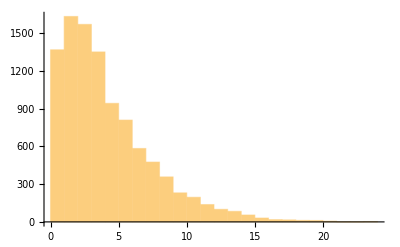

```mathematica
Histogram[Length/@randomOutcomes]
```

```mathematica
Probability[outcome≥10,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.0672

#### Figure 4 countries without UAE and Qatar

```mathematica
Module[{graph,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
graph=Subgraph[FacebookGraphReversed,Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]](*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];

actualNumberOfHopMotifs=Length[findAllHopMotifsReversed[graph,vertexToTimeRules]];
Print["actualNumberOfHopMotifs = ",actualNumberOfHopMotifs];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;
]
```

actualNumberOfHopMotifs = 9

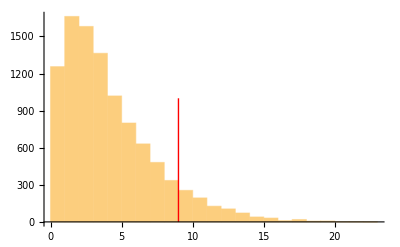

```mathematica
Histogram[Length/@randomOutcomes,Epilog->{Red,Line[{{actualNumberOfHopMotifs,0},{actualNumberOfHopMotifs,1000}}]}]
```

```mathematica
Probability[outcome≥actualNumberOfHopMotifs,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.0871

#### all countries with protests, without UAE and Qatar

```mathematica
Module[{graph,protestTimes,numberOfTrials=1000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
graph=Subgraph[FacebookGraphReversed,countriesWithProtests(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];

actualNumberOfHopMotifs=Length[findAllHopMotifsReversed[graph,vertexToTimeRules]];
Print["actualNumberOfHopMotifs = ",actualNumberOfHopMotifs];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;
]
```

actualNumberOfHopMotifs = 9

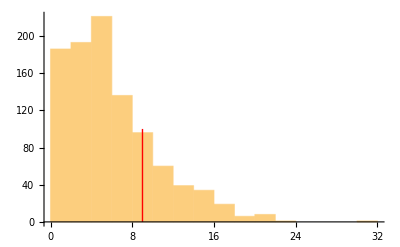

```mathematica
Histogram[Length/@randomOutcomes,Epilog->{Red,Line[{{actualNumberOfHopMotifs,0},{actualNumberOfHopMotifs,100}}]}]
```

```mathematica
Probability[outcome≥actualNumberOfHopMotifs,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.209

#### all countries with protests, with UAE and Qatar

```mathematica
Module[{graph,protestTimes,numberOfTrials=1000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
graph=Subgraph[FacebookGraphReversed,countriesWithProtests~Join~{"United Arab Emirates","Qatar"}(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];

actualNumberOfHopMotifs=Length[findAllHopMotifsReversed[graph,vertexToTimeRules]];
Print["actualNumberOfHopMotifs = ",actualNumberOfHopMotifs];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;
]
```

actualNumberOfHopMotifs = 10

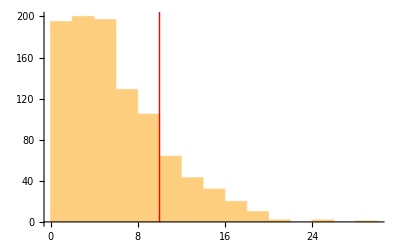

```mathematica
Histogram[Length/@randomOutcomes,Epilog->{Red,Line[{{actualNumberOfHopMotifs,0},{actualNumberOfHopMotifs,1000}}]}]
```

```mathematica
Probability[outcome≥actualNumberOfHopMotifs,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.174

## Shared border network

### shared border graph

```mathematica
borderEdges=Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]];
borderGraph=Graph[borderEdges,VertexLabels->"Name"];
```

### do shared borders close hop motifs? answer: no

10

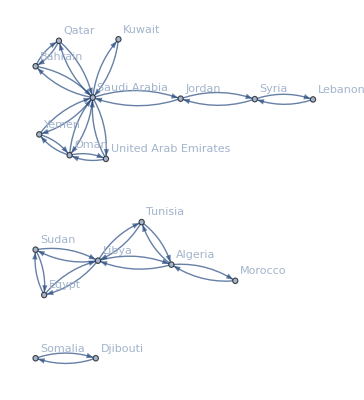

{Algeria->Libya,Algeria->Morocco,Algeria->Tunisia,Bahrain->Qatar,Bahrain->Saudi Arabia,Djibouti->Somalia,Egypt->Libya,Egypt->Sudan,Jordan->Saudi Arabia,Jordan->Syria,Kuwait->Saudi Arabia,Lebanon->Syria,Libya->Algeria,Libya->Egypt,Libya->Sudan,Libya->Tunisia,Morocco->Algeria,Oman->Saudi Arabia,Oman->United Arab Emirates,Oman->Yemen,Qatar->Bahrain,Qatar->Saudi Arabia,Saudi Arabia->Bahrain,Saudi Arabia->Jordan,Saudi Arabia->Kuwait,Saudi Arabia->Oman,Saudi Arabia->Qatar,Saudi Arabia->United Arab Emirates,Saudi Arabia->Yemen,Somalia->Djibouti,Sudan->Egypt,Sudan->Libya,Syria->Jordan,Syria->Lebanon,Tunisia->Algeria,Tunisia->Libya,United Arab Emirates->Oman,United Arab Emirates->Saudi Arabia,Yemen->Oman,Yemen->Saudi Arabia}

```mathematica
Module[{(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];
fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];


borderEdges=Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]];
borderGraph=Graph[borderEdges,VertexLabels->"Name"];

facebookHopMotifs=findAllHopMotifsReversed[fbGraph,vertexToTimeRules];
Print[Length[facebookHopMotifs]];
Print[borderGraph];
EdgeList[borderGraph]

]
```

```mathematica
"upstream"->"downstream"/.facebookHopMotifs
```

{Egypt->Bahrain,Egypt->Bahrain,Egypt->Bahrain,Jordan->Oman,Jordan->Bahrain,Jordan->Oman,Sudan->Bahrain,Tunisia->Jordan,Tunisia->Oman,Yemen->Bahrain}

How many border edges point from an upstream country to a downstream country in the Facebook hop motifs? Zero.

```mathematica
Intersection[{"Algeria"->"Libya","Algeria"->"Morocco","Algeria"->"Tunisia","Bahrain"->"Qatar","Bahrain"->"Saudi Arabia","Djibouti"->"Somalia","Egypt"->"Libya","Egypt"->"Sudan","Jordan"->"Saudi Arabia","Jordan"->"Syria","Kuwait"->"Saudi Arabia","Lebanon"->"Syria","Libya"->"Algeria","Libya"->"Egypt","Libya"->"Sudan","Libya"->"Tunisia","Morocco"->"Algeria","Oman"->"Saudi Arabia","Oman"->"United Arab Emirates","Oman"->"Yemen","Qatar"->"Bahrain","Qatar"->"Saudi Arabia","Saudi Arabia"->"Bahrain","Saudi Arabia"->"Jordan","Saudi Arabia"->"Kuwait","Saudi Arabia"->"Oman","Saudi Arabia"->"Qatar","Saudi Arabia"->"United Arab Emirates","Saudi Arabia"->"Yemen","Somalia"->"Djibouti","Sudan"->"Egypt","Sudan"->"Libya","Syria"->"Jordan","Syria"->"Lebanon","Tunisia"->"Algeria","Tunisia"->"Libya","United Arab Emirates"->"Oman","United Arab Emirates"->"Saudi Arabia","Yemen"->"Oman","Yemen"->"Saudi Arabia"},(*"upstream"->"downstream"/.facebookHopMotifs*){"Egypt"->"Bahrain","Egypt"->"Bahrain","Egypt"->"Bahrain","Jordan"->"Oman","Jordan"->"Bahrain","Jordan"->"Oman","Sudan"->"Bahrain","Tunisia"->"Jordan","Tunisia"->"Oman","Yemen"->"Bahrain"}]
```

{}

```mathematica
{"upstream","downstream"}/.facebookHopMotifs
```

{{Egypt,Bahrain},{Egypt,Bahrain},{Egypt,Bahrain},{Jordan,Oman},{Jordan,Bahrain},{Jordan,Oman},{Sudan,Bahrain},{Tunisia,Jordan},{Tunisia,Oman},{Yemen,Bahrain}}

### what fraction of countries with protests bordered one that already had protests?

#### just countries in Fig. 4: 7 out of the 16 countries shown in Fig. 4 (excluding UAE and Qatar) shared a border with at least one country with protests (p-value 0.02)

```mathematica
Module[{coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=1000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];

fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];

(*borderEdgesDirected=Flatten[Table[UndirectedEdge@@Identity[{c,#}]&/@Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]],
{c,countries}],1]~Join~({"Qatar"<->"Saudi Arabia"})*)

Table[(*UndirectedEdge@@Identity[{c,#}]&/@*){c,Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]],c/.rescaledProtestOutbreakDatesRulesAll,Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]/.rescaledProtestOutbreakDatesRulesAll,((c/.rescaledProtestOutbreakDatesRulesAll)>#)&/@(Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]/.rescaledProtestOutbreakDatesRulesAll)},
{c,countries}]
]
```

{{Algeria,{Libya,Morocco,Tunisia},0.0149457,{0.0828804,0.0869565,0.},{False,False,True}},{Bahrain,{},0.0788043,{},{}},{Djibouti,{Somalia},0.0557065,{0.0557065},{False}},{Egypt,{Libya,Sudan},0.0516304,{0.0828804,0.0584239},{False,False}},{Jordan,{Saudi Arabia,Syria},0.0366848,{0.118207,0.112772},{False,False}},{Kuwait,{Saudi Arabia},0.0855978,{0.118207},{False}},{Lebanon,{Syria},0.0964674,{0.112772},{False}},{Libya,{Algeria,Egypt,Sudan,Tunisia},0.0828804,{0.0149457,0.0516304,0.0584239,0.},{True,True,True,True}},{Morocco,{Algeria},0.0869565,{0.0149457},{True}},{Oman,{Saudi Arabia,Yemen},0.0407609,{0.118207,0.0543478},{False,False}},{Saudi Arabia,{Jordan,Kuwait,Oman,Yemen},0.118207,{0.0366848,0.0855978,0.0407609,0.0543478},{True,True,True,True}},{Somalia,{Djibouti},0.0557065,{0.0557065},{False}},{Sudan,{Egypt,Libya},0.0584239,{0.0516304,0.0828804},{True,False}},{Syria,{Jordan,Lebanon},0.112772,{0.0366848,0.0964674},{True,True}},{Tunisia,{Algeria,Libya},0.,{0.0149457,0.0828804},{False,False}},{Yemen,{Oman,Saudi Arabia},0.0543478,{0.0407609,0.118207},{True,False}}}

```mathematica
Last/@rescaledProtestOutbreakDatesRules
```

{Algeria→0.0149457,Bahrain→0.0788043,Djibouti→0.0557065,Egypt→0.0516304,Iraq→1.,Israel→0.201087,Jordan→0.0366848,Kuwait→0.0855978,Lebanon→0.0964674,Libya→0.0828804,Mauritania→0.09375,Morocco→0.0869565,Oman→0.0407609,Palestinian Territory→0.850543,Saudi Arabia→0.118207,Somalia→0.0557065,Sudan→0.0584239,Syria→0.112772,Tunisia→0.,Yemen→0.0543478}

```mathematica
Sort@rescaledProtestOutbreakDatesRulesAll
```

{Albania→2.,Algeria→0.0149457,Bahrain→0.0788043,Djibouti→0.0557065,Egypt→0.0516304,Iran→2.,Iraq→1.,Israel→0.201087,Jordan→0.0366848,Kuwait→0.0855978,Lebanon→0.0964674,Libya→0.0828804,Mauritania→0.09375,Morocco→0.0869565,Oman→0.0407609,Palestinian Territory→0.850543,Qatar→2.,Saudi Arabia→0.118207,Somalia→0.0557065,Sudan→0.0584239,Syria→0.112772,Tunisia→0.,United Arab Emirates→2.,Yemen→0.0543478}

True/False values for whether a bordering country started to protest earlier:

```mathematica
Module[{neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=1000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];

fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];

(*borderEdgesDirected=Flatten[Table[UndirectedEdge@@Identity[{c,#}]&/@Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]],
{c,countries}],1]~Join~({"Qatar"<->"Saudi Arabia"})*)


(*{First[#],Last[#]}&/@*)
geographicNeighborProtestedAlready=Table[(*UndirectedEdge@@Identity[{c,#}]&/@*)
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c,
(*neighbors,c/.rescaledProtestOutbreakDatesRulesAll,neighbors/.vertexToTimeRules,*)

((c/.rescaledProtestOutbreakDatesRulesAll)>#)&/@(neighbors/.vertexToTimeRules)}

,{c,countries}]
]
```

{{Algeria,{False,False,True}},{Bahrain,{False,False}},{Djibouti,{False}},{Egypt,{False,False}},{Jordan,{False,False}},{Kuwait,{False}},{Lebanon,{False}},{Libya,{True,True,True,True}},{Morocco,{True}},{Oman,{False,False}},{Saudi Arabia,{True,True,True,True,True}},{Somalia,{False}},{Sudan,{True,False}},{Syria,{True,True}},{Tunisia,{False,False}},{Yemen,{True,False}}}

```mathematica
Tally[Or@@Last[#]&/@geographicNeighborProtestedAlready]
```

{{True,7},{False,9}}

```mathematica
{Count[Last[#],True],Count[Last[#],False]}&/@geographicNeighborProtestedAlready
```

{{1,2},{0,2},{0,1},{0,2},{0,2},{0,1},{0,1},{4,0},{1,0},{0,2},{5,0},{0,1},{1,1},{2,0},{0,2},{1,1}}

```mathematica
GatherBy[{First[#],Or@@Last[#]}&/@geographicNeighborProtestedAlready,Last]
```

{{{Algeria,True},{Libya,True},{Morocco,True},{Saudi Arabia,True},{Sudan,True},{Syria,True},{Yemen,True}},{{Bahrain,False},{Djibouti,False},{Egypt,False},{Jordan,False},{Kuwait,False},{Lebanon,False},{Oman,False},{Somalia,False},{Tunisia,False}}}

```mathematica
First/@First[%]
```

{Algeria,Libya,Morocco,Saudi Arabia,Sudan,Syria,Yemen}

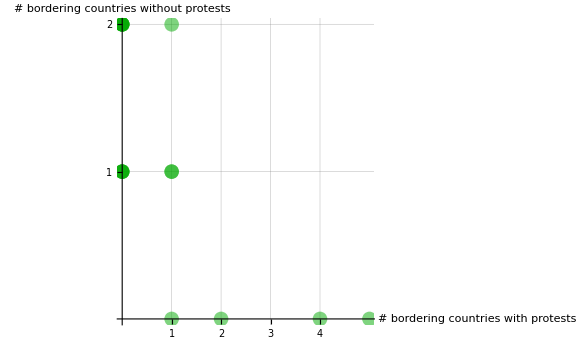

```mathematica
ListPlot[{Count[Last[#],True],Count[Last[#],False]}&/@geographicNeighborProtestedAlready,PlotStyle->{Darker@Green,Opacity[.5]},PlotMarkers->{●,15},ImagePadding->Automatic,ImageSize->Large,Ticks->{Range[4],Range[2]},GridLines->{Range[4],Range[2]},AxesLabel->{"# bordering countries\nwith protests","# bordering countries\nwithout protests"}]
```

Only 7 out of 16 countries (Algeria,Libya,Morocco,Saudi Arabia,Sudan,Syria,Yemen) shared a border with a country that already had protests. Note that we are using geographic borders, and we are also considering Bahrain to border Qatar and Saudi Arabia given the close distance.

```mathematica
rescaledProtestOutbreakDates
```

{{Tunisia,0.},{Algeria,0.0149457},{Jordan,0.0366848},{Oman,0.0407609},{Egypt,0.0516304},{Yemen,0.0543478},{Bahrain,0.0788043},{Libya,0.0828804},{Syria,0.112772},{Saudi Arabia,0.118207},{Djibouti,0.0557065},{Iraq,1.},{Israel,0.201087},{Kuwait,0.0855978},{Mauritania,0.09375},{Morocco,0.0869565},{Palestinian Territory,0.850543},{Somalia,0.0557065},{Sudan,0.0584239},{Lebanon,0.0964674}}

#### all countries with protests: 11 out of all 20 countries with protests shared a border with at least one country that already had protests (p-value 0.02)

```mathematica
Module[{neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=1000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=countriesWithProtests(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*);

fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];

fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];

(*borderEdgesDirected=Flatten[Table[UndirectedEdge@@Identity[{c,#}]&/@Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]],
{c,countries}],1]~Join~({"Qatar"<->"Saudi Arabia"})*)


(*{First[#],Last[#]}&/@*)
geographicNeighborProtestedAlready=Table[(*UndirectedEdge@@Identity[{c,#}]&/@*)
neighbors=
If[c=="Palestinian Territory",Intersection[countries,{"Jordan","Israel","Egypt"}],Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c,
(*neighbors,c/.rescaledProtestOutbreakDatesRulesAll,neighbors/.vertexToTimeRules,*)

((c/.rescaledProtestOutbreakDatesRulesAll)>#)&/@(neighbors/.vertexToTimeRules)}

,{c,countries}]
]
```

{{Algeria,{False,False,False,True}},{Bahrain,{False,False}},{Djibouti,{False}},{Egypt,{False,False,False}},{Iraq,{True,True,True,True}},{Israel,{True,True,True,True}},{Jordan,{False,False,False,False}},{Kuwait,{False,False}},{Lebanon,{False,False}},{Libya,{True,True,True,True}},{Mauritania,{True}},{Morocco,{True}},{Oman,{False,False}},{Palestinian Territory,{True,True,True}},{Saudi Arabia,{False,True,True,True,True,True}},{Somalia,{False}},{Sudan,{True,False}},{Syria,{False,False,True,True}},{Tunisia,{False,False}},{Yemen,{True,False}}}

```mathematica
Tally[Or@@Last[#]&/@geographicNeighborProtestedAlready]
```

{{True,11},{False,9}}

```mathematica
ListPlot[{Count[Last[#],True],Count[Last[#],False]}&/@geographicNeighborProtestedAlready,PlotStyle->{Darker@Green,Opacity[.5]},PlotMarkers->{●,15},ImagePadding->Automatic,ImageSize->Large,Ticks->{Range[4],Range[2]},GridLines->{Range[4],Range[2]},AxesLabel->{"# bordering countries\nwith protests","# bordering countries\nwithout protests"}]
```

#### test for statistical significance on the countries in Figure 4 (excluding UAE and Qatar): 7 out of the 16 countries shown in Fig. 4 (excluding UAE and Qatar) shared a border with at least one country with protests (p-value 0.02)

```mathematica
Module[{(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];

fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];

randomOutcomes=Reap[
Do[
vertexToTimeRules=Thread[countries->RandomReal[{0,1},Length[countries]]];
Sow[Count[Or@@Last[#]&/@
Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c,
(*neighbors,c/.rescaledProtestOutbreakDatesRulesAll,neighbors/.vertexToTimeRules,*)

((c/.rescaledProtestOutbreakDatesRulesAll)>#)&/@(neighbors/.vertexToTimeRules)}

,{c,countries}]
,True]]
,{numberOfTrials}]
]⟦2,1⟧;
];//Timing
```

{464.904,Null}

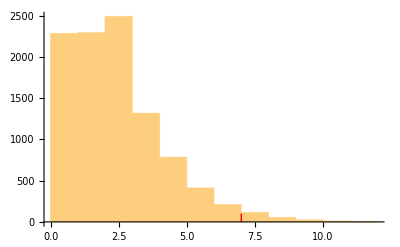

```mathematica
Histogram[randomOutcomes,Epilog->{Red,Line[{{7,0},{7,100}}]}]
```

```mathematica
Probability[outcome≥7,outcome\[Distributed]EmpiricalDistribution[randomOutcomes]]//N
```

0.0203

#### test for statistical significance on the countries in Figure 4 (excluding UAE and Qatar): p-value 0.02

```mathematica
Module[{(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=countriesWithProtests(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*);

fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];

fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];

randomOutcomes=Reap[
Do[
vertexToTimeRules=Thread[countries->RandomReal[{0,1},Length[countries]]];
Sow[Count[Or@@Last[#]&/@
Table[
neighbors=
If[c=="Palestinian Territory",Intersection[countries,{"Jordan","Israel","Egypt"}],Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c,
(*neighbors,c/.rescaledProtestOutbreakDatesRulesAll,neighbors/.vertexToTimeRules,*)

((c/.rescaledProtestOutbreakDatesRulesAll)>#)&/@(neighbors/.vertexToTimeRules)}

,{c,countries}]
,True]]
,{numberOfTrials}]
]⟦2,1⟧;
];//Timing
```

{587.985,Null}

```mathematica
Histogram[randomOutcomes,Epilog->{Red,Line[{{7,0},{7,100}}]}]
```

-Graphics-

```mathematica
Probability[outcome≥7,outcome\[Distributed]EmpiricalDistribution[randomOutcomes]]//N
```

0.0203

#### test significance against null model with randomized links

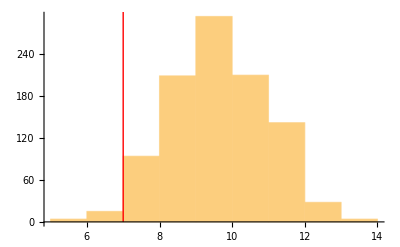

0.981

```mathematica
Module[{randomizedGraph,(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=1000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

(*fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];
fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];*)
borderGraph=Graph[Union@Flatten[Table[
neighbors=
If[c=="Palestinian Territory",Intersection[countries,{"Jordan","Israel","Egypt"}],Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]],VertexLabels->"Name"];

randomOutcomesBorder=Reap[
Do[
(*vertexToTimeRules=Thread[countries->RandomReal[{0,1},Length[countries]]];*)
randomizedGraph=rewireEdgesDirectedGraph[borderGraph,4 EdgeCount[borderGraph]];
Sow[Count[Or@@Last[#]&/@
Table[
neighbors=Complement[VertexInComponent[randomizedGraph,c,1],{c}];

{c,
(*neighbors,c/.rescaledProtestOutbreakDatesRulesAll,neighbors/.vertexToTimeRules,*)

((c/.rescaledProtestOutbreakDatesRulesAll)>#)&/@(neighbors/.vertexToTimeRules)}

,{c,countries}]
,True]]
,{numberOfTrials}]
]⟦2,1⟧;
];
Print[Histogram[randomOutcomesBorder,Epilog->{Red,Line[{{7,0},{7,1000}}]}]];
Probability[outcome≥7,outcome\[Distributed]EmpiricalDistribution[randomOutcomesBorder]]//N
```

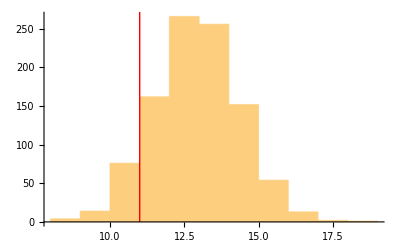

0.906

```mathematica
Module[{randomizedGraph,(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=1000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=countriesWithProtests(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*);

(*fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];
fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];*)
borderGraph=Graph[Union@Flatten[Table[
neighbors=
If[c=="Palestinian Territory",Intersection[countries,{"Jordan","Israel","Egypt"}],Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]],VertexLabels->"Name"];

randomOutcomesBorder=Reap[
Do[
(*vertexToTimeRules=Thread[countries->RandomReal[{0,1},Length[countries]]];*)
randomizedGraph=rewireEdgesDirectedGraph[borderGraph,4 EdgeCount[borderGraph]];
Sow[Count[Or@@Last[#]&/@
Table[
neighbors=Complement[VertexInComponent[randomizedGraph,c,1],{c}];

{c,
(*neighbors,c/.rescaledProtestOutbreakDatesRulesAll,neighbors/.vertexToTimeRules,*)

((c/.rescaledProtestOutbreakDatesRulesAll)>#)&/@(neighbors/.vertexToTimeRules)}

,{c,countries}]
,True]]
,{numberOfTrials}]
]⟦2,1⟧;
];
Print[Histogram[randomOutcomesBorder,Epilog->{Red,Line[{{11,0},{11,1000}}]}]];
Probability[outcome≥11,outcome\[Distributed]EmpiricalDistribution[randomOutcomesBorder]]//N
```

If you randomize the shared-border edges, keeping in- and out-degree fixed, then we find that the real network has fewer outcomes than the randomized ones.

### geographic network hop motifs

#### compute hop motifs in the shared border network

```mathematica
Module[{(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

(*fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];
fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];
*)

borderEdges=Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]];
borderGraph=Graph[borderEdges,VertexLabels->"Name"];

borderHopMotifs=findAllHopMotifsReversed[borderGraph,vertexToTimeRules]

]
```

{{upstream→Algeria,intermediate→Libya,downstream→Egypt},{upstream→Tunisia,intermediate→Libya,downstream→Egypt},{upstream→Bahrain,intermediate→Saudi Arabia,downstream→Kuwait},{upstream→Jordan,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Jordan,intermediate→Saudi Arabia,downstream→Kuwait},{upstream→Jordan,intermediate→Saudi Arabia,downstream→Oman},{upstream→Jordan,intermediate→Syria,downstream→Lebanon},{upstream→Oman,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Oman,intermediate→Saudi Arabia,downstream→Kuwait},{upstream→Yemen,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Yemen,intermediate→Saudi Arabia,downstream→Kuwait}}

```mathematica
Length@%
```

11

#### also say that Bahrain borders UAE

```mathematica
Module[{(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

(*fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];
fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];
*)

borderEdges=Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","United Arab Emirates","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="United Arab Emirates",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]];
borderGraph=Graph[borderEdges,VertexLabels->"Name"];

borderHopMotifs=findAllHopMotifsReversed[borderGraph,vertexToTimeRules]

]
```

{{upstream→Algeria,intermediate→Libya,downstream→Egypt},{upstream→Tunisia,intermediate→Libya,downstream→Egypt},{upstream→Bahrain,intermediate→Saudi Arabia,downstream→Kuwait},{upstream→Jordan,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Jordan,intermediate→Saudi Arabia,downstream→Kuwait},{upstream→Jordan,intermediate→Saudi Arabia,downstream→Oman},{upstream→Jordan,intermediate→Syria,downstream→Lebanon},{upstream→Oman,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Oman,intermediate→Saudi Arabia,downstream→Kuwait},{upstream→Oman,intermediate→United Arab Emirates,downstream→Bahrain},{upstream→Yemen,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Yemen,intermediate→Saudi Arabia,downstream→Kuwait}}

```mathematica
Length@%
```

12

Hop motifs in the FB and border networks:

```mathematica
Dataset[Association/@Intersection[facebookHopMotifs,borderHopMotifs]][SortBy[#intermediate&]]
```

upstream | intermediate | downstream
Jordan | Saudi Arabia | Bahrain
Jordan | Saudi Arabia | Oman
Yemen | Saudi Arabia | Bahrain
2 levels | 3rows |  | Dataset[{__Association}]

#### statistical significance

```mathematica
Module[{(*randomOutcomes,*)neighbors,coordinatesBG,borderGraph,borderEdges,borderEdgesDirected,fbEdges,fbGraph,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
countries=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

(*fbEdges=Property[#,"type"->"Facebook"]&/@EdgeList[Subgraph[FacebookGraphReversed,countries]];
fbGraph=SetProperty[Graph[fbEdges],{VertexLabels->"Name",EdgeStyle->RGBColor[{59,89,152}/256],ImageSize->Medium}];
*)

borderEdges=Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]];
borderGraph=Graph[borderEdges,VertexLabels->"Name"];

borderHopMotifs=findAllHopMotifsReversed[borderGraph,vertexToTimeRules]

]
```

```mathematica
Length[borderHopMotifs]
```

11

#### intersection with Facebook hop motifs:

```mathematica
Intersection[facebookHopMotifs,borderHopMotifs]
```

{{upstream→Jordan,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Jordan,intermediate→Saudi Arabia,downstream→Oman},{upstream→Yemen,intermediate→Saudi Arabia,downstream→Bahrain}}

```mathematica
Dataset[Association/@Intersection[facebookHopMotifs,borderHopMotifs]][SortBy[#intermediate&]]
```

upstream | intermediate | downstream
Jordan | Saudi Arabia | Bahrain
Jordan | Saudi Arabia | Oman
Yemen | Saudi Arabia | Bahrain
2 levels | 3rows |  | Dataset[{__Association}]

Facebook hop motifs that are not border hop motifs:

```mathematica
Complement[facebookHopMotifs,borderHopMotifs]
```

{{upstream→Egypt,intermediate→Kuwait,downstream→Bahrain},{upstream→Egypt,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Egypt,intermediate→United Arab Emirates,downstream→Bahrain},{upstream→Jordan,intermediate→Egypt,downstream→Oman},{upstream→Sudan,intermediate→Saudi Arabia,downstream→Bahrain},{upstream→Tunisia,intermediate→Egypt,downstream→Jordan},{upstream→Tunisia,intermediate→Egypt,downstream→Oman}}

```mathematica
Dataset[Association/@Complement[facebookHopMotifs,borderHopMotifs]][SortBy[#intermediate&]]
```

upstream | intermediate | downstream
Jordan | Egypt | Oman
Tunisia | Egypt | Jordan
Tunisia | Egypt | Oman
Egypt | Kuwait | Bahrain
Egypt | Saudi Arabia | Bahrain
Sudan | Saudi Arabia | Bahrain
Egypt | United Arab Emirates | Bahrain
2 levels | 7rows |  | Dataset[{__Association}]

Border hop motifs that are not Facebook hop motifs:

```mathematica
Dataset[Association/@Complement[borderHopMotifs,facebookHopMotifs]][SortBy[#intermediate&]]
```

upstream | intermediate | downstream
Algeria | Libya | Egypt
Tunisia | Libya | Egypt
Bahrain | Saudi Arabia | Kuwait
Jordan | Saudi Arabia | Kuwait
Oman | Saudi Arabia | Bahrain
Oman | Saudi Arabia | Kuwait
Yemen | Saudi Arabia | Kuwait
Jordan | Syria | Lebanon
2 levels | 8rows |  | Dataset[{__Association}]

### compute statistical significance of getting 11 hop motifs in the border dataset by randomizing the protest start dates

```mathematica
TableForm[{{"countries in Fig. 4, with UAE & Qatar",11,0.0979},{"countries in Fig. 4, without UAE & Qatar",11,0.0049},{"all 20 countries with protests",16,0.0022},{"all 20 countries with protests, plus UAE and Qatar",16,0.0294}},TableHeadings->{None,{"countries","# hop motifs in border graph","p-value"}}]
```

countries | # hop motifs in border graph | p-value
countries in Fig. 4, with UAE & Qatar | 11 | 0.0979
countries in Fig. 4, without UAE & Qatar | 11 | 0.0049
all 20 countries with protests | 16 | 0.0022
all 20 countries with protests, plus UAE and Qatar | 16 | 0.0294

#### border network, Figure 4 countries, with UAE and Qatar: 11 hop motifs, p-value 0.098

```mathematica
Module[{graph,neighbors,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
(*graph=Subgraph[FacebookGraphReversed,Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]](*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];*)

countries=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

graph=Graph[Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]],VertexLabels->"Name"];
actualNumberOfHopMotifs=Length@findAllHopMotifsReversed[graph,vertexToTimeRules]
]
```

11

```mathematica
Module[{graph,neighbors,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
(*graph=Subgraph[FacebookGraphReversed,Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]](*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];*)

countries=Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

graph=Graph[Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]],VertexLabels->"Name"];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;
]//Timing
```

{136.728,Null}

```mathematica
Length/@randomOutcomes
```

{8,1,13,0,5,3,2,5,4,8,4,0,3,10,2,1,6,1,3,4,2,0,2,11,5,2,5,2,4,2,9,7,0,0,2,4,1,3,1,2,3,16,1,7,4,8,14,10,15,5,1,6,3,8,5,3,1,7,1,16,5,8,0,1,1,0,4,1,1,1,0,5,3,3,1,7,10,12,0,5,11,5,10,2,4,7,5,2,2,9,11,13,2,5,4,8,5,14,6,4,4,1,1,3,0,4,9,8,4,3,1,10,11,1,2,4,0,1,4,5,2,1,3,1,7,0,9,12,3,14,7,1,4,1,5,3,1,3,5,0,2,9,15,4,7,14,7,9,1,10,6,1,1,3,2,4,9,10,1,2,3,2,5,3,3,12,0,2,7,7,5,2,2,2,4,4,7,7,8,3,7,2,12,2,10,1,4,2,3,3,8,6,13,4,5,2,3,12,2,1,7,2,7,7,3,9,7,3,2,4,1,9,18,5,2,1,1,2,2,1,3,2,2,11,2,5,14,4,8,4,11,2,13,10,12,8,4,5,1,3,3,4,15,4,7,18,2,2,0,9,7,8,9,11,1,9,12,1,3,0,1,1,5,7,2,2,14,4,9,8,3,4,6,2,8,6,14,10,5,5,10,10,3,6,2,4,16,9,11,1,2,1,2,2,12,2,3,5,3,8,2,6,0,7,7,3,2,14,2,9,5,1,4,2,3,3,3,3,14,3,7,5,3,1,5,6,10,10,15,1,6,4,1,3,2,8,2,10,6,3,9,3,0,2,3,9,2,12,2,5,8,8,4,4,0,3,2,1,5,4,4,9,3,4,5,1,1,6,9,3,6,5,6,3,4,2,4,14,6,0,2,13,2,11,15,7,3,0,3,2,5,9,2,1,4,5,10,0,3,5,1,2,1,1,1,1,2,1,6,14,9,4,3,11,5,9,6,2,5,8,1,8,9,8,3,2,15,2,4,1,4,5,3,1,4,9,2,3,5,6,3,8,17,8,2,5,1,1,4,7,0,10,9,1,2,2,12,2,2,5,1,4,7,5,4,3,1,0,4,1,1,3,16,3,4,2,0,4,5,5,0,1,11,6,1,2,4,13,3,1,5,2,1,10,3,1,12,2,8,9,8,3,0,1,0,2,5,12,6,16,0,9,12,3,4,4,9,7,3,6,2,4,10,15,3,1,1,8,10,0,10,3,0,0,5,10,3,4,1,1,1,5,12,4,9,7,8,10,0,9,2,14,4,7,5,2,5,2,5,10,2,1,4,3,11,3,0,14,0,2,6,3,4,5,2,3,3,10,10,0,5,2,4,9,11,3,2,9,5,7,10,1,3,1,8,3,9,8,10,8,5,6,6,3,9,11,2,14,2,2,7,9,2,5,5,6,4,7,11,8,12,0,5,13,1,13,4,8,5,8,2,1,5,6,5,1,13,2,3,11,13,3,4,8,15,6,2,2,7,5,6,4,14,9,6,4,15,4,6,8,5,6,9,1,2,9,3,4,1,0,1,1,9,4,3,12,9,8,16,8,6,0,2,7,7,1,4,11,4,3,11,5,3,0,5,5,1,9,2,3,4,5,6,3,4,2,8,5,9,8,3,3,2,5,1,12,3,2,1,11,12,3,3,12,13,5,1,6,0,4,1,1,12,9,3,1,7,1,3,3,6,0,5,0,3,2,10,1,2,9,13,14,0,9,9,11,9,7,4,6,9,16,4,0,1,1,1,9,4,12,9,1,7,5,2,8,14,3,6,7,13,7,0,0,7,2,9,11,5,3,10,3,5,1,2,8,17,7,2,4,4,2,2,7,8,4,2,4,6,12,9,1,1,15,1,2,1,14,4,5,7,6,2,15,4,7,2,2,6,6,2,4,1,8,10,2,4,6,1,0,6,3,8,4,1,1,8,7,8,5,2,4,14,8,2,3,2,10,14,3,2,6,11,5,4,2,8,5,1,7,3,3,16,4,4,3,2,10,2,2,2,1,5,1,13,1,4,0,9,0,4,8,14,4,2,6,8,9,7,3,0,2,4,2,3,7,1,3,2,9,8,1,10,6,9,9,8,4,2,4,2,1,6,2,1,6,11,1,7,15,5,2,11,13,1,5,3,9,8,12,5,4,1,1,0,3,13,0,1,3,1,6,9,9,2,2,3,9,4,7,1,2,1,3,1,3,1,8,3,3,0,1,5,11,2,7,3,4,3,1,1,11,14,8,1,10,8,0,3,2,3,2,4,4,5,7,6,4,0,1}

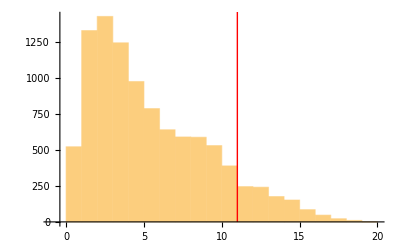

```mathematica
Histogram[Length/@randomOutcomes,{1},Epilog->{Red,Line[{{11,0},{11,10000}}]}]
```

```mathematica
Probability[outcome≥11,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.0979

#### border network, Figure 4 countries, without UAE and Qatar: 11 hop motifs, p-value 0.0049

```mathematica
Module[{graph,neighbors,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
(*graph=Subgraph[FacebookGraphReversed,Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]](*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];*)

countries=Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]];

graph=Graph[Union@Flatten[Table[
neighbors=Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]],VertexLabels->"Name"];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;

actualNumberOfHopMotifs=Length@findAllHopMotifsReversed[graph,vertexToTimeRules];
]//Timing
```

{104.491,Null}

```mathematica
actualNumberOfHopMotifs
```

11

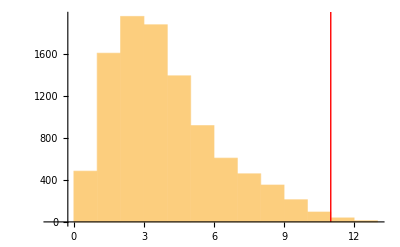

```mathematica
Histogram[Length/@randomOutcomes,{1},Epilog->{Red,Line[{{actualNumberOfHopMotifs,0},{actualNumberOfHopMotifs,10000}}]}]
```

```mathematica
Probability[outcome≥actualNumberOfHopMotifs,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.0049

#### all countries with protests; 16 hop motifs, p-value 0.0022

```mathematica
Module[{graph,neighbors,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
(*graph=Subgraph[FacebookGraphReversed,Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]](*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];*)

countries=countriesWithProtests(*Cases[countriesWithProtests,Except["Palestinian Territory"]]*)(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*);

graph=Graph[Union@Flatten[Table[
neighbors=
If[c=="Palestinian Territory",Intersection[countries,{"Jordan","Israel","Egypt"}],Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]],VertexLabels->"Name"];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;

actualNumberOfHopMotifs=Length@findAllHopMotifsReversed[graph,vertexToTimeRules];
]//Timing
```

{280.158,Null}

```mathematica
actualNumberOfHopMotifs
```

16

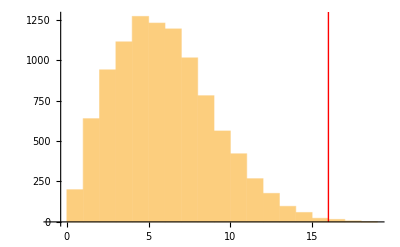

```mathematica
Histogram[Length/@randomOutcomes,{1},Epilog->{Red,Line[{{actualNumberOfHopMotifs,0},{actualNumberOfHopMotifs,10000}}]}]
```

```mathematica
Probability[outcome≥actualNumberOfHopMotifs,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.0022

#### all countries with protests, plus UAE and Qatar: 16 hop motifs, p-value 0.0294

```mathematica
Module[{graph,neighbors,countries,protestTimes,numberOfTrials=10000,vertexToTimeRules=rescaledProtestOutbreakDatesRulesAll},
(*graph=Subgraph[FacebookGraphReversed,Cases[countriesWithProtests~Join~{"United Arab Emirates","Qatar"},Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]](*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*)];*)

countries=countriesWithProtests~Join~{"United Arab Emirates","Qatar"}(*Cases[countriesWithProtests(*~Join~{"United Arab Emirates","Qatar"}*),Except["Palestinian Territory"|"Iraq"|"Israel"|"Mauritania"]]*);

graph=Graph[Union@Flatten[Table[
neighbors=
If[c=="Palestinian Territory",Intersection[countries,{"Jordan","Israel","Egypt"}],Intersection[countries,CountryData[#,"Name"]&/@CountryData[c,"BorderingCountries"]]];
If[c=="Bahrain",neighbors=neighbors~Join~{"Qatar","Saudi Arabia"}];
If[c=="Qatar",neighbors=neighbors~Join~{"Bahrain"}];
If[c=="Saudi Arabia",neighbors=neighbors~Join~{"Bahrain"}];

{c->#,#->c}&/@neighbors

,{c,countries}]],VertexLabels->"Name"];

randomOutcomes=Reap[
Do[
protestTimes=Thread[VertexList[graph]->RandomReal[{0,1},Length[VertexList[graph]]]];
Sow[findAllHopMotifsReversed[graph,protestTimes]];
,{numberOfTrials}]
]⟦2,1⟧;

actualNumberOfHopMotifs=Length@findAllHopMotifsReversed[graph,vertexToTimeRules];
]//Timing
```

{336.052,Null}

```mathematica
actualNumberOfHopMotifs
```

16

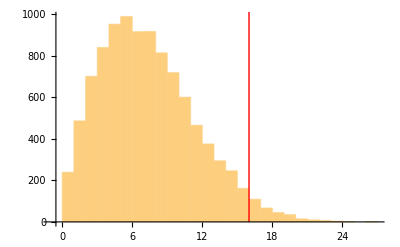

```mathematica
Histogram[Length/@randomOutcomes,{1},Epilog->{Red,Line[{{actualNumberOfHopMotifs,0},{actualNumberOfHopMotifs,10000}}]}]
```

```mathematica
Probability[outcome≥actualNumberOfHopMotifs,outcome\[Distributed]EmpiricalDistribution[Length/@randomOutcomes]]//N
```

0.0294

### Hop motif significance: summary

Facebook hop motifs:

countries | # hop motifs in Facebook graph | p-value
countries in Fig. 4, with UAE & Qatar | 10 | 0.0672
countries in Fig. 4, without UAE & Qatar | 9 | 0.0871
all 20 countries with protests | 16 | 0.209
all 20 countries with protests, plus UAE and Qatar | 10 | 0.174

Border hop motifs:

countries | # hop motifs in border graph | p-value
countries in Fig. 4, with UAE & Qatar | 11 | 0.0979
countries in Fig. 4, without UAE & Qatar | 11 | 0.0049
all 20 countries with protests | 16 | 0.0022
all 20 countries with protests, plus UAE and Qatar | 16 | 0.0294